```mathematica
Clear["Global`*"];
```

```mathematica
B[β_?NumericQ]=(Gamma[(β+2)/2]/Gamma[(β+1)/2])^2;
A[β_?NumericQ]=2/Gamma[(β+1)/2] B[β]^((β+1)/2);
p[s_?NumericQ,β_?NumericQ]:=A[β] s^β ⅇ^(-B[β] s^2)
```

```mathematica
ξsb[ξb_?NumericQ]:=Gamma[ξb+1/2]/Gamma[ξb];
NV[L_?NumericQ,ξb_?NumericQ, f_?NumericQ]:= (1-f)L+((ξsb[ξb]/(√ξb))^-2-1) (L/f)^2
```

```mathematica
tablemod[{fileNND_String, fileNV_String, fileL_String}]:=Module[{nnd,filename,nlmNND,nv,nlmNV,l}, 
nnd=Import[fileNND, "Table"];
filename=StringDelete[fileNND,"/home/xierr/Desktop/pato_all/pato_new_all/pato_new/Portugese_NND_results/"|".txt"];
nlmNND=NonlinearModelFit[nnd,p[s,β],β,s];
nv=Import[fileNV, "Table"];
nlmNV=NonlinearModelFit[nv,NV[L,ξb,f],{ξb,f},L];
l=Import[fileL];
{filename,ToExpression[l],N[nlmNND["BestFitParameters"][[1,2]]],N[nlmNV["BestFitParameters"][[2,2]]],N[nlmNV["BestFitParameters"][[1,2]]],N[nlmNND["RSquared"]],N[nlmNV["RSquared"]]}]
```

```mathematica
(*plotmod[file_String]:=Module[{nnd}, 
nnd=Import[file, "Table"];
ListPlot[nnd,PlotMarkers->Automatic]]*)
```

```mathematica
filesNND=FileNames["*.txt","/home/xierr/Desktop/pato_all/pato_new_all/pato_new/Portugese_NND_results"];
filesNV=FileNames["*.txt","/home/xierr/Desktop/pato_all/pato_new_all/pato_new/Portugese_NV_results"];
filesL=FileNames["*.txt","/home/xierr/Desktop/pato_all/pato_new_all/pato_new/Portugese_L_results"];
```

```mathematica
CloseKernels[];LaunchKernels[4];
DistributeDefinitions[tablemod,filesNND,filesNV,filesL];
```

```mathematica
TableForm[ParallelMap[tablemod[#]&,Transpose[{filesNND,filesNV,filesL}]]/.{x_Real:>NumberForm[x,{15,4}]},TableHeadings->{None,{"Sequence","⟨L⟩","β","f","ξ̄","R_NND^2","R_NV^2"}}]
```

Sequence | ⟨L⟩ | β | f | ξ̄ | R_NND^2 | R_NV^2
11299-8 | 4.7975 | 0.2354 | 0.7324 | 310.6429 | 0.9621 | 0.9995
12579-8 | 4.8962 | 0.1622 | 0.7211 | 453.9375 | 0.9754 | 0.9991
13092-8 | 4.9734 | 0.1420 | 0.7993 | 404.6513 | 0.9700 | 0.9996
13093-8 | 4.9255 | 0.1151 | 0.7435 | 625.4573 | 0.9656 | 0.9988
13630-8 | 5.0363 | 0.1121 | 0.7365 | 1586.3774 | 0.9668 | 0.9973
14296-8 | 4.8982 | 0.1958 | 0.7432 | 921.4718 | 0.9697 | 0.9989
14620-8 | 4.9264 | 0.1318 | 0.7789 | 624.8442 | 0.9728 | 0.9991
14621-8 | 4.9488 | 0.1512 | 0.7691 | 2480.1463 | 0.9621 | 0.9984
14622-8 | 4.9675 | 0.1164 | 0.7824 | 1290.3357 | 0.9673 | 0.9986
15668-8 | 4.8269 | 0.3966 | 0.8155 | 438.2581 | 0.9494 | 0.9991
15674-8 | 4.4833 | 0.3822 | 0.8746 | 785.9110 | 0.9588 | 0.9995
16111-8 | 4.9530 | 0.1233 | 0.8020 | 354.4523 | 0.9700 | 0.9999
16214-8 | 4.9377 | 0.1089 | 0.7694 | 228.6871 | 0.9683 | 0.9997
16218-8 | 4.9387 | 0.1405 | 0.7270 | 499.8066 | 0.9648 | 0.9992
16219-8 | 4.9031 | 0.1531 | 0.7743 | 703.7989 | 0.9582 | 0.9994
16384-8 | 4.9618 | 0.2632 | 0.8352 | 1681.3093 | 0.9712 | 0.9992
16385-8 | 4.5401 | 0.5838 | 0.8259 | 8282.8489 | 0.9819 | 0.9988
16425-8 | 4.5249 | 0.3120 | 0.7773 | 551.1226 | 0.9801 | 0.9996
16428-8 | 4.6391 | 0.3285 | 0.7756 | 283.7465 | 0.9735 | 0.9999
16429-8 | 4.6205 | 0.3480 | 0.8066 | 1150.6681 | 0.9844 | 0.9993
16443-8 | 4.8065 | 0.3356 | 0.7736 | 417.9908 | 0.9760 | 0.9998
16571-8 | 4.4748 | 0.5112 | 0.8517 | 817.5483 | 0.9732 | 0.9995
16633-8 | 4.4368 | 0.5762 | 0.8801 | 728.1635 | 0.9531 | 0.9998
16922-8 | 5.0275 | 0.1766 | 0.8044 | 1003.1515 | 0.9517 | 0.9997
17005-8 | 4.7304 | 0.2581 | 0.8272 | 647.5322 | 0.9779 | 0.9998
17036-8 | 5.0964 | 0.1361 | 0.8324 | 1338.7207 | 0.9641 | 0.9995
17186-8 | 5.1961 | 0.2180 | 0.7696 | 306.1068 | 0.9459 | 0.9998
17193-8 | 4.3419 | 0.4944 | 0.8082 | 560.8769 | 0.9848 | 0.9996
17503-8 | 4.7822 | 0.3036 | 0.8212 | 211.8439 | 0.9879 | 0.9999
17515-8 | 4.7809 | 0.3041 | 0.8289 | 965.3711 | 0.9738 | 0.9998
17534-8 | 4.7662 | 0.4672 | 0.7019 | 1258.0814 | 0.9826 | 0.9965
17591-8 | 4.4162 | 0.6855 | 0.8123 | 692.0862 | 0.9726 | 0.9989
17610-8 | 4.1291 | 0.5025 | 0.8081 | 903.7116 | 0.9815 | 0.9979
17639-8 | 4.6057 | 0.3908 | 0.8164 | 395.0295 | 0.9682 | 0.9997
17895-8 | 5.0559 | 0.1266 | 0.7937 | 486.8349 | 0.9638 | 0.9997
17927-8 | 4.7447 | 0.1931 | 0.7642 | 362.3338 | 0.9726 | 0.9998
17962-8 | 4.4435 | 0.3816 | 0.7904 | 363.3870 | 0.9832 | 0.9993
18026-8 | 4.4969 | 0.3974 | 0.8372 | 329.8945 | 0.9772 | 0.9999
18082-8 | 4.2969 | 0.6739 | 0.8533 | 1307.2178 | 0.9757 | 0.9986
18167-8 | 4.5513 | 0.5735 | 0.8667 | 776.9674 | 0.9802 | 0.9995
18220-8 | 4.8397 | 0.2736 | 0.8093 | 664.2190 | 0.9793 | 0.9998
18330-8 | 4.9001 | 0.2048 | 0.8072 | 761.2089 | 0.9756 | 0.9996
18519-8 | 4.8025 | 0.2001 | 0.9327 | 835.8192 | 0.9548 | 0.9661
18528-8 | 5.0203 | 0.2161 | 0.8629 | 2020.0519 | 0.9671 | 0.9966
18974-8 | 4.8063 | 0.2337 | 0.8531 | 364.3658 | 0.9704 | 0.9971
19046-8 | 4.6158 | 0.3185 | 0.7333 | 947.8196 | 0.9653 | 0.9890
19062-8 | 4.6762 | 0.4915 | 0.8840 | 1464.9553 | 0.9724 | 0.9504
19189-8 | 4.5893 | 0.4444 | 0.8500 | 2087.2909 | 0.9704 | 0.9979
19375-8 | 4.9827 | 0.1360 | 0.8769 | 2550.4489 | 0.9609 | 0.9853
19532-8 | 4.6803 | 0.3047 | 0.8156 | 212.1317 | 0.9838 | 0.9999
19641-8 | 4.4310 | 0.4571 | 0.8536 | 2253.3588 | 0.9565 | 0.9947
19947-8 | 4.6718 | 0.3103 | 0.8185 | 4783.6506 | 0.9718 | 0.9915
19974-8 | 4.8928 | 0.1152 | 0.7956 | 2097.0640 | 0.9665 | 0.9971
20042-8 | 4.8321 | 0.2132 | 0.8720 | 716.3148 | 0.9641 | 0.9861
20103-8 | 4.8354 | 0.3043 | 0.8234 | 1747.9313 | 0.9773 | 0.9969
20142-8 | 4.5295 | 0.2747 | 0.7675 | 221.9777 | 0.9822 | 0.9999
20149-8 | 4.6244 | 0.5722 | 0.8275 | 730.2043 | 0.9835 | 0.9980
20482-8 | 4.6156 | 0.4352 | 0.8984 | 2172.5904 | 0.9759 | 0.8872
20495-8 | 4.6245 | 0.2669 | 0.8830 | 2576.2966 | 0.9813 | 0.9624
20508-8 | 4.7370 | 0.2613 | 0.7733 | 661.9092 | 0.9703 | 0.9996
20574-8 | 4.7980 | 0.3386 | 0.7920 | 1105.2170 | 0.9788 | 0.9997
20581-8 | 4.4428 | 0.5146 | 0.7746 | 676.4556 | 0.9853 | 0.9978
20582-8 | 4.9600 | 0.2267 | 0.8450 | 822.5306 | 0.9529 | 0.9944
20701-8 | 4.7042 | 0.3386 | 0.8112 | 676.3115 | 0.9715 | 0.9952
20725-8 | 4.6806 | 0.2884 | 0.7927 | 569.4888 | 0.9842 | 0.9997
20783-8 | 4.7523 | 0.2574 | 0.7813 | 443.5468 | 0.9758 | 0.9997
20841-8 | 4.4559 | 0.3142 | 0.7905 | 408.9416 | 0.9891 | 0.9998
20874-8 | 4.5178 | 0.2986 | 0.8052 | 120.5895 | 0.9864 | 0.9999
20940-8 | 4.4988 | 0.3394 | 0.8192 | 930.8292 | 0.9834 | 0.9990
20998-8 | 4.8215 | 0.1018 | 0.8137 | 1018.1769 | 0.9631 | 0.9985
20999-8 | 4.8228 | 0.1648 | 0.8307 | 1450.5496 | 0.9749 | 0.9976
21011-8 | 4.6529 | 0.3979 | 0.8208 | 137.1011 | 0.9780 | 0.9995
21209-8 | 4.6395 | 0.2324 | 0.7843 | 331.7199 | 0.9816 | 0.9999
21283-8 | 4.6670 | 0.5471 | 0.8334 | 2261.2207 | 0.9846 | 0.9980
21287-8 | 4.3922 | 0.8893 | 0.8588 | 689.8435 | 0.9821 | 0.9807
21289-8 | 4.4604 | 0.5653 | 0.8388 | 1311.9627 | 0.9852 | 0.9967
21290-8 | 4.7380 | 0.2536 | 0.7836 | 477.4814 | 0.9832 | 0.9998
21406-8 | 4.7824 | 0.2047 | 0.7788 | 483.7986 | 0.9765 | 0.9997
21429-8 | 5.8177 | 0.4108 | 0.5784 | 104.2819 | 0.9196 | 0.9994
21545-8 | 4.4223 | 0.6966 | 0.8411 | 1940.5019 | 0.9833 | 0.9939
21563-8 | 4.5631 | 0.4928 | 0.8443 | 743.7544 | 0.9939 | 0.9992
21567-8 | 5.0061 | 0.2720 | 0.8229 | 2134.5143 | 0.9869 | 0.9994
21581-8 | 4.6047 | 0.2387 | 0.8331 | 1054.5658 | 0.9769 | 0.9989
21684-8 | 4.9426 | 0.1200 | 0.8177 | 558.2594 | 0.9715 | 0.9998
21779-8 | 4.7143 | 0.2267 | 0.7928 | 922.5471 | 0.9743 | 0.9983
21780-8 | 4.4015 | 0.6708 | 0.8361 | 1290.7388 | 0.9820 | 0.9982
21786-8 | 4.6023 | 0.3381 | 0.8614 | 2126.9410 | 0.9796 | 0.9990
21799-8 | 4.4781 | 0.4214 | 0.5399 | 1180.3017 | 0.9771 | 0.9893
21855-8 | 4.5909 | 0.3343 | 0.7691 | 1097.2497 | 0.9827 | 0.9976
21911-8 | 4.5078 | 0.3288 | 0.8669 | 1806.5178 | 0.9649 | 0.9996
21961-8 | 4.7095 | 0.2979 | 0.7563 | 971.2897 | 0.9871 | 0.9994
22015-8 | 4.7229 | 0.4247 | 0.8255 | 787.1242 | 0.9863 | 0.9996
22299-8 | 4.5668 | 0.2538 | 0.8187 | 164.2085 | 0.9886 | 0.9999
22330-8 | 4.6471 | 0.4666 | 0.7219 | 2620.0001 | 0.9763 | 0.9734
22378-8 | 4.8136 | 0.2047 | 0.8672 | 2263.9682 | 0.9246 | 0.9891
22395-8 | 4.7192 | 0.1976 | 0.6525 | 1443.4514 | 0.9707 | 0.9639
22412-8 | 4.5918 | 0.7987 | 0.6633 | 1811.6508 | 0.9623 | 0.9805
22468-8 | 4.6840 | 0.1963 | 0.8246 | 2215.9547 | 0.9382 | 0.9350
22469-8 | 4.4843 | 0.3451 | 0.8946 | 2989.4370 | 0.9738 | 0.9748
22508-8 | 4.5297 | 0.4486 | 0.8339 | 1619.7566 | 0.9767 | 0.9995
22509-8 | 4.7453 | 0.2390 | 0.8259 | 427.4388 | 0.9757 | 0.9995
22614-8 | 4.6809 | 0.3442 | 0.8325 | 667.9438 | 0.9614 | 0.9948
22615-8 | 4.8882 | 0.1542 | 0.6541 | 1622.1775 | 0.9561 | 0.9818
22616-8 | 4.8122 | 0.2876 | 0.8012 | 88.0629 | 0.9470 | 0.9965
22622-8 | 4.9658 | 0.3247 | 0.8018 | 609.9015 | 0.9768 | 0.9995
22632-8 | 4.5328 | 0.4344 | 0.7964 | 1993.2894 | 0.9834 | 0.9740
22634-8 | 4.5816 | 0.2463 | 0.8387 | 3458.4190 | 0.9462 | 0.9530
22647-8 | 4.7273 | 0.1433 | 0.9170 | 2712.0359 | 0.9780 | 0.9265
22648-8 | 4.7462 | 0.2658 | 0.9548 | 2668.8674 | 0.9519 | 0.6408
22658-8 | 4.6496 | 0.4456 | 0.8043 | 343.7448 | 0.9782 | 0.9997
22678-8 | 4.3546 | 0.4771 | 0.7445 | 1259.4638 | 0.9787 | 0.9709
22679-8 | 4.5937 | 0.2784 | 0.8139 | 541.2115 | 0.9820 | 0.9941
22723-8 | 4.6862 | 0.2836 | 0.7696 | 2062.7099 | 0.9736 | 0.9873
22729-8 | 4.7430 | 0.3905 | 0.7358 | 553.9762 | 0.9731 | 0.9981
22730-8 | 4.9335 | 0.7056 | 0.9671 | 3800.7875 | 0.9694 | 0.3865
22742-8 | 4.4691 | 0.2998 | 0.8525 | 459.1688 | 0.9682 | 0.9995
22772-8 | 4.5946 | 0.3043 | 0.8289 | 2648.0523 | 0.9807 | 0.9542
22801-8 | 4.3518 | 0.5217 | 0.7895 | 620.8953 | 0.9795 | 0.9976
22802-8 | 4.9212 | 0.2203 | 0.8724 | 2829.1073 | 0.9407 | 0.8942
22817-8 | 4.4680 | 0.6760 | 0.9224 | 276.2941 | 0.9572 | 0.9773
22826-8 | 4.5500 | 0.3793 | 0.8443 | 910.6431 | 0.9728 | 0.9995
22870-8 | 4.7418 | 0.5819 | 0.9153 | 1823.1481 | 0.9854 | 0.9790
22898-8 | 4.7391 | 0.3651 | 0.9054 | 2005.1141 | 0.9708 | 0.8167
22907-8 | 4.5946 | 0.2125 | 0.9216 | 2715.1523 | 0.9748 | 0.9413
22969-8 | 4.7185 | 0.1500 | 0.8308 | 1417.1672 | 0.9615 | 0.9055
22970-8 | 4.6679 | 0.4328 | 0.9353 | 1911.5826 | 0.9864 | 0.9458
22977-8 | 4.6697 | 0.2735 | 0.7549 | 671.0930 | 0.9711 | 0.9995
23105-8 | 4.3394 | 0.3194 | 0.8099 | 2211.0074 | 0.9787 | 0.9928
23109-8 | 4.5419 | 0.5892 | 0.8133 | 1676.1728 | 0.9745 | 0.9908
23110-8 | 4.5860 | 0.3830 | 0.8433 | 1515.3265 | 0.9648 | 0.9855
23133-8 | 5.0839 | 0.1312 | 0.5479 | 580.7054 | 0.9459 | 0.9982
23145-8 | 4.7975 | 0.2827 | 0.8279 | 908.2228 | 0.9799 | 0.9998
23156-8 | 4.5118 | 0.5937 | 0.7549 | 1596.9822 | 0.9480 | 0.9713
23201-8 | 4.8522 | 0.1353 | 0.8022 | 547.4410 | 0.9479 | 0.9995
23203-8 | 4.7786 | 0.3513 | 0.8062 | 757.6353 | 0.9699 | 0.9995
23345-8 | 4.6364 | 0.2993 | 0.8332 | 1570.5990 | 0.9665 | 0.9972
23346-8 | 4.8881 | 0.2734 | 0.8867 | 2442.7199 | 0.9638 | 0.9805
23400-8 | 4.8064 | 0.2886 | 0.8391 | 1178.4910 | 0.9749 | 0.9993
23442-8 | 4.7005 | 0.2737 | 0.8206 | 1612.1209 | 0.9788 | 0.9898
23486-8 | 4.7154 | 0.4811 | 0.8467 | 3156.4840 | 0.9783 | 0.9939
23525-8 | 4.7830 | 0.4417 | 0.8448 | 4289.3611 | 0.9705 | 0.9751
23526-8 | 4.5916 | 0.2162 | 0.8039 | 1483.0636 | 0.9769 | 0.9983
23620-8 | 4.5143 | 0.4616 | 0.7378 | 288.1268 | 0.9870 | 0.9993
23621-8 | 4.6990 | 0.3618 | 0.5916 | 301.6654 | 0.9818 | 0.9995
23687-8 | 4.9819 | 0.2982 | 0.8003 | 902.5009 | 0.9755 | 0.9998
23851-8 | 4.8366 | 0.1001 | 0.7692 | 894.9337 | 0.9410 | 0.9979
23879-8 | 4.5465 | 0.3910 | 0.7884 | 2546.1242 | 0.9634 | 0.9966
23919-8 | 4.9164 | 0.1991 | 0.8149 | 576.8863 | 0.9722 | 0.9998
23961-8 | 4.6828 | 0.1161 | 0.7680 | 288.4540 | 0.9602 | 0.9975
24129-8 | 4.5797 | 0.2613 | 0.7665 | 387.7491 | 0.9770 | 0.9901
24164-8 | 4.6232 | 0.2848 | 0.7303 | 923.3382 | 0.9808 | 0.9993
24190-8 | 5.1357 | 0.1731 | 0.7836 | 920.1493 | 0.9717 | 0.9994
24245-8 | 4.4387 | 0.4176 | 0.7831 | 1520.0130 | 0.9766 | 0.9961
24289-0 | 4.6910 | 0.2365 | 0.8645 | 3388.7394 | 0.9775 | 0.9909
24291-8 | 4.3883 | 0.1522 | 0.7548 | 416.9919 | 0.9731 | 0.9984
24319-8 | 4.6825 | 0.3130 | 0.7906 | 675.0264 | 0.9788 | 0.9997
24338-8 | 4.9180 | 0.1346 | 0.7625 | 1625.0818 | 0.9767 | 0.9985
24339-8 | 5.0297 | 0.1766 | 0.7298 | 861.3731 | 0.9686 | 0.9975
24344-8 | 4.8185 | 0.2308 | 0.8094 | 949.8372 | 0.9754 | 0.9994
24401-8 | 4.6487 | 0.2966 | 0.7590 | 727.2418 | 0.9804 | 0.9997
24411-8 | 4.2345 | 0.6706 | 0.8231 | 581.0125 | 0.9763 | 0.9985
24412-8 | 5.1286 | 0.1376 | 0.7876 | 1484.1701 | 0.9659 | 0.9980
24455-8 | 5.1326 | 0.2363 | 0.7852 | 684.1562 | 0.9402 | 0.9998
24462-8 | 5.0211 | 0.2810 | 0.7230 | 3139.9026 | 0.9599 | 0.9878
24463-8 | 4.7353 | 0.2256 | 0.7884 | 435.8880 | 0.9686 | 0.9994
24464-8 | 4.7172 | 0.2150 | 0.7910 | 1543.3820 | 0.9681 | 0.9983
24508-8 | 4.4721 | 0.2420 | 0.8627 | 1858.3452 | 0.9707 | 0.9991
24514-8 | 4.8948 | 0.2372 | 0.8135 | 1031.0706 | 0.9618 | 0.9970
24533-8 | 4.9670 | 0.1629 | 0.7545 | 903.9834 | 0.9635 | 0.9976
24619-8 | 4.7569 | 0.3819 | 0.8611 | 434.1550 | 0.9746 | 0.9960
24620-8 | 5.0700 | 0.1362 | 0.8164 | 5342.8776 | 0.9794 | 0.9895
24625-8 | 4.5954 | 0.3379 | 0.7993 | 690.2652 | 0.9795 | 0.9998
24646-8 | 4.3904 | 0.3475 | 0.7821 | 646.5014 | 0.9852 | 0.9987
24657-8 | 4.8325 | 0.2264 | 0.8036 | 841.7513 | 0.9677 | 0.9990
24710-8 | 4.8384 | 0.1760 | 0.8024 | 722.6570 | 0.9831 | 0.9992
24833-8 | 4.7611 | 0.2824 | 0.8646 | 1980.5471 | 0.9802 | 0.9981
24843-8 | 5.4031 | 0.2734 | 0.6831 | 1529.4991 | 0.9505 | 0.9723
24845-8 | 4.8058 | 0.1923 | 0.9680 | 1962.3062 | 0.9209 | 0.7590
24846-8 | 4.9252 | 0.3967 | 0.8156 | 2416.4001 | 0.9670 | 0.9599
24847-8 | 4.5204 | 0.3589 | 0.6684 | 252.1022 | 0.9851 | 0.9995
24919-8 | 5.1044 | 0.1741 | 0.7983 | 1141.6658 | 0.9770 | 0.9999
24957-8 | 4.7648 | 0.1991 | 0.8298 | 1203.1350 | 0.9632 | 0.9992
25113-8 | 5.0095 | 0.1790 | 0.8471 | 1706.1776 | 0.9501 | 0.9988
25114-8 | 4.7107 | 0.2138 | 0.8246 | 643.0782 | 0.9709 | 0.9993
25148-8 | 4.5041 | 0.3669 | 0.8426 | 1405.9322 | 0.9829 | 0.9993
25238-8 | 4.7186 | 0.2332 | 0.7991 | 2165.9683 | 0.9574 | 0.9429
25239-8 | 4.8148 | 0.1937 | 0.8376 | 1563.8277 | 0.9517 | 0.9802
25241-8 | 4.5138 | 0.4624 | 0.8742 | 2511.1648 | 0.9841 | 0.9915
25313-8 | 4.7400 | 0.2257 | 0.8040 | 948.9197 | 0.9755 | 0.9995
25330-8 | 4.7079 | 0.1895 | 0.8022 | 441.0225 | 0.9738 | 0.9999
25336-8 | 4.5057 | 0.5336 | 0.8090 | 2495.3474 | 0.9811 | 0.9900
25436-8 | 4.7474 | 0.5228 | 0.9245 | 1861.2972 | 0.9633 | 0.9614
25437-8 | 4.6484 | 0.1850 | 0.8330 | 393.7537 | 0.9766 | 0.9993
25479-8 | 4.9360 | 0.1658 | 0.7911 | 236.6775 | 0.9559 | 0.9998
25537-8 | 4.8680 | 0.2865 | 0.7938 | 1229.7985 | 0.9758 | 0.9995
25593-8 | 4.6503 | 0.2637 | 0.8205 | 302.6117 | 0.9796 | 0.9998
25594-8 | 4.6565 | 0.1643 | 0.8766 | 1090.1822 | 0.9774 | 0.9976
25641-8 | 4.9121 | 0.2030 | 0.8296 | 718.6972 | 0.9787 | 0.9999
25667-8 | 4.7636 | 0.3445 | 0.8158 | 678.0107 | 0.9784 | 0.9993
25697-8 | 5.0270 | 0.1353 | 0.8658 | 1399.6520 | 0.9603 | 0.9870
25840-8 | 4.5303 | 0.4975 | 0.8535 | 1801.7785 | 0.9818 | 0.9986
25844-8 | 4.7982 | 0.3184 | 0.8537 | 1503.0004 | 0.9745 | 0.9776
25845-8 | 4.9021 | 0.1244 | 0.7690 | 680.8132 | 0.9543 | 0.9985
25846-8 | 5.0989 | 0.1778 | 0.8249 | 548.1651 | 0.9633 | 0.9985
25898-8 | 5.0572 | 0.1314 | 0.8211 | 1677.4669 | 0.9704 | 0.9987
25925-8 | 4.4041 | 0.3261 | 0.8424 | 1777.4286 | 0.9716 | 0.9991
25934-8 | 5.0318 | 0.1419 | 0.8811 | 1676.5421 | 0.9732 | 0.9972
25945-8 | 4.7978 | 0.2567 | 0.7912 | 1523.2772 | 0.9804 | 0.9998
25987-8 | 4.5490 | 0.2507 | 0.8583 | 846.3317 | 0.9694 | 0.9995
26017-8 | 4.7009 | 0.2602 | 0.7904 | 590.4347 | 0.9666 | 0.9995
26025-8 | 4.7217 | 0.2623 | 0.7880 | 304.2392 | 0.9747 | 0.9998
26103-8 | 4.6443 | 0.2766 | 0.8128 | 831.7499 | 0.9754 | 0.9997
26110-8 | 4.7698 | 0.2865 | 0.8043 | 1051.0376 | 0.9764 | 0.9998
26326-8 | 4.2353 | 0.3536 | 0.7846 | 327.8890 | 0.9871 | 0.9993
26338-8 | 4.9897 | 0.1656 | 0.7537 | 2444.9954 | 0.9816 | 0.9993
26371-8 | 4.8217 | 0.2219 | 0.7971 | 726.2738 | 0.9810 | 0.9996
26411-8 | 4.3380 | 0.4736 | 0.7664 | 200.0006 | 0.9761 | 0.9984
26605-8 | 4.8363 | 0.1400 | 0.8282 | 601.6762 | 0.9662 | 0.9997
26676-8 | 4.5453 | 0.5906 | 0.8066 | 494.0728 | 0.9729 | 0.9988
26848-8 | 4.6387 | 0.3886 | 0.8368 | 1326.0488 | 0.9667 | 0.9993
26850-8 | 5.0332 | 0.2113 | 0.7990 | 804.6274 | 0.9713 | 0.9998
26913-8 | 4.6856 | 0.3836 | 0.8320 | 1571.5360 | 0.9801 | 0.9960
26988-8 | 4.7507 | 0.2626 | 0.8129 | 583.5278 | 0.9692 | 0.9998
27084-8 | 4.7755 | 0.1077 | 0.8077 | 282.8526 | 0.9756 | 0.9997
27155-8 | 4.8285 | 0.4682 | 0.7992 | 382.4203 | 0.9869 | 0.9995
27236-0 | 3.7373 | 0.1963 | 0.8046 | 1644.6425 | 0.9799 | 0.9981
27242-8 | 5.7543 | 0.5976 | 0.7436 | 196.4603 | 0.9041 | 0.9996
27276-8 | 4.6923 | 0.3669 | 0.8836 | 1383.2455 | 0.9848 | 0.9942
27311-8 | 4.4565 | 0.3377 | 0.8405 | 657.4390 | 0.9614 | 0.9990
27364-8 | 4.5687 | 0.3886 | 0.7767 | 308.4064 | 0.9779 | 0.9999
27388-8 | 5.1412 | 0.1822 | 0.8647 | 550.1220 | 0.9544 | 0.9866
27390-8 | 4.7229 | 0.1639 | 0.8754 | 2596.2199 | 0.9516 | 0.8838
27412-8 | 4.7736 | 0.2662 | 0.8059 | 1314.9340 | 0.9807 | 0.9977
27413-8 | 4.6688 | 0.3757 | 0.9630 | 2589.0909 | 0.9593 | 0.8337
27497-8 | 4.7622 | 0.2522 | 0.8323 | 1394.1175 | 0.9635 | 0.9870
27498-8 | 4.9115 | 0.3901 | 0.7172 | 1238.4465 | 0.9708 | 0.9982
27535-8 | 4.4085 | 0.5418 | 0.7691 | 228.2814 | 0.9832 | 0.9997
27540-8 | 4.8956 | 0.1719 | 0.8346 | 2333.1899 | 0.9674 | 0.9835
27541-8 | 4.7354 | 0.2931 | 0.7996 | 859.9829 | 0.9735 | 0.9996
27542-8 | 4.9123 | 0.1049 | 0.8619 | 6297.5637 | 0.9762 | 0.9777
27543-8 | 4.8432 | 0.2069 | 0.7945 | 392.5509 | 0.9640 | 0.9969
27544-8 | 4.5083 | 0.5221 | 0.9004 | 2062.6807 | 0.9825 | 0.9842
27545-8 | 4.7023 | 0.3167 | 0.8020 | 865.9753 | 0.9368 | 0.9911
27599-8 | 4.1139 | 0.5527 | 0.7490 | 710.7020 | 0.9935 | 0.9987
27637-8 | 4.8834 | 0.2439 | 0.8088 | 763.6779 | 0.9800 | 0.9998
27689-8 | 4.8595 | 0.1022 | 0.8148 | 980.3998 | 0.9774 | 0.9981
27691-8 | 4.8254 | 0.2414 | 0.8523 | 1632.0633 | 0.9749 | 0.9986
27715-8 | 5.2199 | 0.1491 | 0.8187 | 1201.5783 | 0.9731 | 0.9992
27725-8 | 4.3809 | 0.7390 | 0.8484 | 1060.5446 | 0.9592 | 0.9995
27762-8 | 4.7680 | 0.2043 | 0.7315 | 267.5069 | 0.9694 | 0.9997
27820-8 | 4.8869 | 0.1859 | 0.8374 | 1340.3646 | 0.9635 | 0.9975
27940-8 | 4.2918 | 0.4950 | 0.8662 | 1262.6716 | 0.9853 | 0.9985
27941-8 | 4.7915 | 0.2633 | 0.9714 | 1242.1768 | 0.9745 | 0.8509
27964-8 | 4.9911 | 0.1349 | 0.7929 | 835.2436 | 0.9649 | 0.9997
27992-8 | 4.8763 | 0.1310 | 0.7957 | 852.5737 | 0.9771 | 0.9983
28122-0 | 4.3685 | 0.5898 | 0.8626 | 588.9693 | 0.9718 | 0.9989
28127-8 | 4.5782 | 0.3198 | 0.7856 | 544.1647 | 0.9848 | 0.9998
28128-8 | 4.8913 | 0.1318 | 0.8331 | 639.8159 | 0.9695 | 0.9994
28154-8 | 4.6335 | 0.4891 | 0.8257 | 546.9863 | 0.9752 | 0.9992
28155-8 | 4.8194 | 0.3031 | 0.8270 | 1013.8120 | 0.9664 | 0.9993
28201-8 | 4.7135 | 0.1521 | 0.7972 | 543.8130 | 0.9716 | 0.9987
28206-8 | 4.7436 | 0.2737 | 0.7990 | 342.2574 | 0.9713 | 0.9996
28310-8 | 4.6743 | 0.3232 | 0.7848 | 1038.1836 | 0.9755 | 0.9995
28341-8 | 5.0152 | 0.1817 | 0.7843 | 1116.6265 | 0.9661 | 0.9996
28348-8 | 4.6283 | 0.1043 | 0.2147 | 1042.6797 | 0.9711 | 0.9989
28354-8 | 4.3260 | 0.3752 | 0.7488 | 672.4764 | 0.9834 | 0.9981
2837-8 | 4.5022 | 0.4058 | 0.8173 | 668.0192 | 0.9848 | 0.9994
28399-0 | 4.2726 | 0.7565 | 0.7664 | 148.3690 | 0.9700 | 0.9999
28414-8 | 4.3088 | 0.4277 | 0.8374 | 730.9960 | 0.9840 | 0.9998
28526-8 | 4.8624 | 0.2367 | 0.8420 | 1215.3886 | 0.9874 | 0.9984
28584-8 | 4.8276 | 0.1939 | 0.7637 | 1216.5925 | 0.9776 | 0.9995
28639-8 | 4.6336 | 0.2678 | 0.8048 | 192.6035 | 0.9804 | 0.9999
28640-8 | 4.7908 | 0.4257 | 0.8696 | 1244.6288 | 0.9892 | 0.9789
28691-8 | 5.2295 | 0.1643 | 0.8245 | 910.1874 | 0.9699 | 0.9980
28692-8 | 4.4882 | 0.2852 | 0.7896 | 554.5662 | 0.9823 | 0.9986
28707-8 | 5.0322 | 0.2770 | 0.8076 | 390.7002 | 0.9733 | 0.9993
28928-8 | 4.7486 | 0.3468 | 0.7994 | 748.2109 | 0.9861 | 0.9995
29039-8 | 4.6098 | 0.4997 | 0.8670 | 2251.3519 | 0.9519 | 0.9938
29040-8 | 4.8406 | 0.2382 | 0.8644 | 2836.9611 | 0.9629 | 0.9982
29120-8 | 4.7681 | 0.2683 | 0.7618 | 504.8733 | 0.9782 | 0.9998
29161-8 | 5.1952 | 0.2679 | 0.8396 | 560.1428 | 0.9767 | 0.9989
29213-8 | 4.9975 | 0.1281 | 0.8321 | 1521.8112 | 0.9644 | 0.9991
29243-8 | 4.8795 | 0.2222 | 0.8307 | 3609.1375 | 0.9713 | 0.9987
29275-8 | 4.8158 | 0.2244 | 0.8146 | 1372.9279 | 0.9723 | 0.9994
29342-8 | 4.9277 | 0.2756 | 0.7912 | 2106.9441 | 0.9784 | 0.9976
29347-8 | 4.8139 | 0.2402 | 0.7904 | 2443.9742 | 0.9806 | 0.9950
29394-8 | 4.3575 | 0.4231 | 0.8331 | 1057.7858 | 0.9788 | 0.9998
29428-8 | 5.0849 | 0.2604 | 0.8079 | 535.8431 | 0.9603 | 0.9993
29435-8 | 4.6408 | 0.2487 | 0.7786 | 523.6479 | 0.9773 | 0.9997
29529-8 | 5.0639 | 0.1749 | 0.8160 | 1021.8986 | 0.9724 | 0.9992
29550-8 | 4.8400 | 0.2179 | 0.8001 | 684.5996 | 0.9747 | 0.9998
29740-8 | 4.6876 | 0.3776 | 0.7819 | 490.2164 | 0.9742 | 0.9997
29804-8 | 5.2568 | 0.2652 | 0.7864 | 94.2245 | 0.9680 | 1.0000
29884-8 | 4.6154 | 0.1216 | 0.7821 | 1404.6439 | 0.9691 | 0.9991
29898-8 | 4.6273 | 0.3291 | 0.8639 | 3387.4558 | 0.9553 | 0.9947
29968-8 | 4.7363 | 0.3440 | 0.8362 | 804.5243 | 0.9826 | 0.9998
29979-8 | 4.6499 | 0.3117 | 0.8369 | 747.3323 | 0.9765 | 0.9996
29996-8 | 4.6735 | 0.2152 | 0.7650 | 665.2974 | 0.9696 | 0.9891
29997-8 | 4.9047 | 0.1768 | 0.7792 | 403.2644 | 0.9727 | 0.9955
29998-8 | 5.2722 | 0.1212 | 0.9800 | 1318.7129 | 0.9587 | 0.5299
29999-8 | 4.8488 | 0.1342 | 0.7878 | 1076.2602 | 0.9769 | 0.9986
30068-8 | 4.5290 | 0.5618 | 0.8604 | 2131.8783 | 0.9537 | 0.9922
30069-8 | 4.7126 | 0.1964 | 0.8433 | 714.0046 | 0.9531 | 0.9929
30070-8 | 4.6924 | 0.1450 | 0.6484 | 1244.8191 | 0.9694 | 0.9954
30071-8 | 4.8950 | 0.1449 | 0.7143 | 1157.2981 | 0.9670 | 0.9982
30091-8 | 4.6313 | 0.3819 | 0.8727 | 2175.4099 | 0.9810 | 0.9978
30161-8 | 4.9467 | 0.3246 | 0.8118 | 1518.3729 | 0.9755 | 0.9993
30176-8 | 4.7624 | 0.2137 | 0.7753 | 363.6707 | 0.9726 | 0.9999
30341-8 | 5.1666 | 0.2723 | 0.8033 | 579.6873 | 0.9812 | 0.9995
30359-8 | 4.6563 | 0.1984 | 0.8205 | 381.9715 | 0.9707 | 0.9998
30404-8 | 4.9216 | 0.1896 | 0.8200 | 1565.8735 | 0.9751 | 0.9991
30413-8 | 4.7022 | 0.3760 | 0.8128 | 638.6840 | 0.9747 | 0.9991
30461-8 | 4.4576 | 0.1954 | 0.7897 | 716.0774 | 0.9801 | 0.9990
30462-8 | 4.3900 | 0.3899 | 0.7880 | 612.6638 | 0.9863 | 0.9987
30510-8 | 4.6477 | 0.3350 | 0.8575 | 1076.4700 | 0.9848 | 0.9987
30543-8 | 4.8362 | 0.3551 | 0.8425 | 1747.6153 | 0.9784 | 0.9983
30566-8 | 4.9564 | 0.1827 | 0.8142 | 794.6546 | 0.9602 | 0.9998
30571-8 | 4.8567 | 0.3729 | 0.7808 | 2396.7367 | 0.9786 | 0.9985
30777-8 | 4.7073 | 0.4286 | 0.8272 | 903.0895 | 0.9802 | 0.9993
30801-8 | 4.8856 | 0.2111 | 0.8135 | 326.6429 | 0.9722 | 0.9998
30805-8 | 4.8711 | 0.3995 | 0.6817 | 1461.5714 | 0.9685 | 0.9335
30806-8 | 4.9954 | 0.1343 | 0.7861 | 921.3680 | 0.9679 | 0.9984
30857-8 | 4.5991 | 0.3719 | 0.8649 | 1890.4494 | 0.9767 | 0.9947
30858-8 | 4.5525 | 0.4081 | 0.7556 | 2092.7574 | 0.9836 | 0.9897
30859-8 | 4.3905 | 0.3846 | 0.8228 | 6314.3234 | 0.9792 | 0.9794
30919-8 | 4.6894 | 0.2957 | 0.8204 | 1270.5659 | 0.9831 | 0.9946
30920-8 | 4.6171 | 0.3943 | 0.8122 | 2499.9546 | 0.9759 | 0.9844
30926-8 | 4.8354 | 0.3038 | 0.8144 | 634.0960 | 0.9840 | 0.9998
30945-8 | 5.2188 | 0.1123 | 0.9144 | 1889.2284 | 0.9059 | 0.8872
30946-8 | 4.9790 | 0.2293 | 0.8211 | 1366.0827 | 0.9820 | 0.9995
30947-8 | 4.5844 | 0.4356 | 0.7938 | 544.0262 | 0.9821 | 0.9995
31093-8 | 4.6146 | 0.3533 | 0.8140 | 1304.0337 | 0.9627 | 0.9923
31166-8 | 4.9114 | 0.2047 | 0.8280 | 2080.2121 | 0.9784 | 0.9964
31190-8 | 4.6565 | 0.2732 | 0.7426 | 452.0948 | 0.9678 | 0.9996
31347-8 | 4.6699 | 0.3250 | 0.8533 | 643.3652 | 0.9826 | 0.9998
31509-8 | 4.4682 | 0.5888 | 0.8215 | 860.0040 | 0.9852 | 0.9999
31573-8 | 5.1168 | 0.2658 | 0.8196 | 2913.7730 | 0.9791 | 0.9976
31575-8 | 4.3307 | 0.7223 | 0.8742 | 2798.9284 | 0.9778 | 0.9709
31576-8 | 4.7856 | 0.3140 | 0.7478 | 1106.1206 | 0.9812 | 0.9954
31654-8 | 5.1269 | 0.1429 | 0.8222 | 1196.5027 | 0.9635 | 0.9982
31656-8 | 5.0137 | 0.1602 | 0.7188 | 166.2532 | 0.9648 | 0.9996
31657-8 | 4.6537 | 0.3440 | 0.7785 | 439.5018 | 0.9752 | 0.9998
31694-8 | 4.6531 | 0.2420 | 0.7828 | 670.1158 | 0.9712 | 0.9995
31695-8 | 4.5583 | 0.4315 | 0.8263 | 1329.7678 | 0.9834 | 0.9890
31696-8 | 4.6710 | 0.3650 | 0.7229 | 665.6005 | 0.9702 | 0.9962
31740-8 | 5.2529 | 0.6111 | 0.5997 | 132.7929 | 0.9625 | 0.9999
31741-8 | 4.3984 | 0.5105 | 0.8866 | 1421.1785 | 0.9780 | 0.9971
31742-8 | 4.5217 | 0.2596 | 0.7165 | 247.1186 | 0.9790 | 0.9992
31743-8 | 4.5339 | 0.6229 | 0.8410 | 613.5891 | 0.9765 | 0.9990
31744-8 | 4.4835 | 0.6095 | 0.8486 | 1629.5026 | 0.9773 | 0.9990
31905-8 | 4.6579 | 0.3613 | 0.8351 | 519.2309 | 0.9791 | 0.9998
31906-8 | 4.6284 | 0.3733 | 0.8701 | 1423.4594 | 0.9807 | 0.9935
31917-8 | 5.0441 | 0.2767 | 0.7598 | 673.9634 | 0.9765 | 0.9997
31971-8 | 4.7206 | 0.2977 | 0.8041 | 975.6177 | 0.9837 | 0.9998
32001-8 | 4.8642 | 0.1519 | 0.8023 | 748.0111 | 0.9716 | 0.9947
32002-8 | 4.7456 | 0.2770 | 0.7853 | 1122.6155 | 0.9773 | 0.9996
32003-8 | 4.8577 | 0.1628 | 0.8025 | 3368.8375 | 0.9724 | 0.9653
32020-8 | 4.5644 | 0.4604 | 0.8009 | 903.9406 | 0.9834 | 0.9996
32072-8 | 4.9500 | 0.1061 | 0.7749 | 530.8076 | 0.9638 | 0.9998
32156-8 | 5.0219 | 0.2369 | 0.8491 | 402.4653 | 0.9730 | 0.9990
32174-8 | 5.2272 | 0.1134 | 0.8417 | 1540.9092 | 0.9551 | 0.9992
32295-8 | 4.3808 | 0.4853 | 0.8450 | 2056.6917 | 0.9874 | 0.9954
32296-8 | 4.8526 | 0.1827 | 0.8440 | 1247.9494 | 0.9755 | 0.9991
32380-8 | 4.9886 | 0.2896 | 0.8041 | 1189.5326 | 0.9784 | 0.9997
32381-8 | 4.7997 | 0.1934 | 0.8172 | 1348.4554 | 0.9755 | 0.9971
32387-8 | 4.8363 | 0.2614 | 0.8621 | 2523.6029 | 0.9682 | 0.9983
32519-8 | 5.2297 | 0.1131 | 0.8142 | 943.9505 | 0.9682 | 0.9996
32586-8 | 4.5211 | 0.1534 | 0.7923 | 1066.2060 | 0.9778 | 0.9992
32645-8 | 4.9160 | 0.1591 | 0.8574 | 4192.7988 | 0.9575 | 0.9935
32646-8 | 4.8576 | 0.2139 | 0.7858 | 929.0111 | 0.9769 | 0.9997
32647-8 | 4.8057 | 0.2657 | 0.7718 | 2225.2184 | 0.9838 | 0.9967
32790-8 | 4.9605 | 0.1351 | 0.8067 | 3357.1853 | 0.9573 | 0.9852
32792-8 | 4.7504 | 0.2500 | 0.8089 | 340.0435 | 0.9732 | 0.9998
32793-8 | 4.7421 | 0.3463 | 0.8463 | 1629.1558 | 0.9815 | 0.9998
32868-8 | 4.5886 | 0.2354 | 0.7984 | 604.0510 | 0.9903 | 0.9967
32869-8 | 4.8785 | 0.1231 | 0.8315 | 2078.5063 | 0.9716 | 0.9995
32871-8 | 4.7168 | 0.2084 | 0.7562 | 628.6954 | 0.9810 | 0.9990
33056-8 | 4.6970 | 0.3446 | 0.8322 | 1353.2178 | 0.9798 | 0.9992
33057-8 | 5.0243 | 0.1298 | 0.8922 | 2595.6900 | 0.9687 | 0.9889
33067-8 | 4.7391 | 0.3059 | 0.7877 | 862.0993 | 0.9744 | 0.9993
33068-8 | 5.1522 | 0.1098 | 0.8076 | 1559.1054 | 0.9701 | 0.9984
33159-8 | 4.7499 | 0.4457 | 0.6252 | 124.0413 | 0.9700 | 0.9998
33182-8 | 4.7201 | 0.1683 | 0.7938 | 518.4581 | 0.9793 | 0.9998
33238-8 | 4.9626 | 0.1563 | 0.7862 | 758.2879 | 0.9751 | 0.9992
33245-8 | 4.9422 | 0.1894 | 0.8472 | 2281.5431 | 0.9565 | 0.9980
33276-8 | 4.7766 | 0.3900 | 0.8097 | 617.9341 | 0.9826 | 0.9972
3333-8 | 4.4787 | 0.5390 | 0.8542 | 1477.1412 | 0.9786 | 0.9973
33377-8 | 5.3178 | 0.1193 | 0.8296 | 878.2074 | 0.9501 | 0.9997
33572-8 | 5.0597 | 0.1685 | 0.7923 | 619.5136 | 0.9740 | 0.9989
33581-8 | 4.9292 | 0.2583 | 0.8002 | 697.9982 | 0.9705 | 0.9995
33588-8 | 4.6150 | 0.3297 | 0.7974 | 620.1559 | 0.9835 | 0.9997
33611-8 | 5.2173 | 0.2762 | 0.7992 | 901.2332 | 0.9654 | 0.9996
33749-8 | 4.8193 | 0.2645 | 0.7968 | 689.7425 | 0.9806 | 0.9995
33788-8 | 4.6974 | 0.3101 | 0.8370 | 865.1601 | 0.9759 | 0.9996
33838-8 | 5.2729 | 0.2301 | 0.6649 | 1794.7284 | 0.9642 | 0.9956
34039-8 | 4.7200 | 0.3388 | 0.8290 | 741.7946 | 0.9769 | 0.9995
34040-8 | 4.7557 | 0.3207 | 0.8362 | 1735.5583 | 0.9617 | 0.9995
34041-8 | 4.7361 | 0.3308 | 0.8225 | 1582.4877 | 0.9655 | 0.9987
34155-0 | 4.3264 | 0.3029 | 0.7757 | 376.1556 | 0.9820 | 0.9998
34275-8 | 4.4703 | 0.3272 | 0.7310 | 1247.4430 | 0.9805 | 0.9991
34276-8 | 4.8499 | 0.2440 | 0.8102 | 305.6359 | 0.9630 | 0.9998
34287-8 | 4.6910 | 0.5618 | 0.8574 | 8141.7671 | 0.9793 | 0.9983
34288-8 | 4.8338 | 0.2656 | 0.8541 | 2702.3743 | 0.9830 | 0.9958
34289-8 | 4.7888 | 0.2119 | 0.8371 | 5816.3726 | 0.9648 | 0.9907
34290-8 | 4.8360 | 0.1063 | 0.8304 | 866.4778 | 0.9641 | 0.9976
34292-8 | 5.1863 | 0.1042 | 0.8188 | 1506.2911 | 0.9716 | 0.9937
34293-8 | 4.3588 | 0.1503 | 0.9590 | 1134.5601 | 0.9698 | 0.8071
34387-8 | 4.8300 | 0.1167 | 0.8021 | 570.3290 | 0.9659 | 0.9996
34388-8 | 5.0561 | 0.2019 | 0.8314 | 1734.7428 | 0.9584 | 0.9982
34621-8 | 5.1478 | 0.2715 | 0.8619 | 1434.2886 | 0.9355 | 0.9323
34623-8 | 4.9999 | 0.1937 | 0.7897 | 1039.0716 | 0.9673 | 0.9993
34625-8 | 4.6390 | 0.3979 | 0.8363 | 2515.3137 | 0.9816 | 0.9920
34626-8 | 4.6088 | 0.4318 | 0.8646 | 1498.0335 | 0.9834 | 0.9957
34718-8 | 4.8576 | 0.3951 | 0.8125 | 1507.8968 | 0.9760 | 0.9962
34719-8 | 4.7824 | 0.2898 | 0.8039 | 634.2763 | 0.9800 | 0.9997
34742-8 | 4.8188 | 0.2670 | 0.8697 | 1858.5666 | 0.9719 | 0.9945
34750-8 | 4.8554 | 0.2103 | 0.7177 | 489.7482 | 0.9719 | 0.9990
34755-8 | 4.9126 | 0.2371 | 0.8399 | 2100.2865 | 0.9668 | 0.9949
34952-8 | 4.9751 | 0.3389 | 0.8290 | 2402.5979 | 0.9568 | 0.9781
34960-8 | 4.5910 | 0.3404 | 0.8440 | 1641.8768 | 0.9764 | 0.9976
34961-8 | 5.0395 | 0.2424 | 0.8533 | 92.9786 | 0.9736 | 0.9998
34963-8 | 4.7004 | 0.3867 | 0.8283 | 698.5504 | 0.9866 | 0.9992
35073-8 | 4.8218 | 0.3474 | 0.8236 | 745.1743 | 0.9845 | 0.9997
35130-8 | 4.7892 | 0.2634 | 0.8011 | 2430.9874 | 0.9626 | 0.9938
35131-8 | 4.6883 | 0.2916 | 0.7306 | 226.8366 | 0.9630 | 0.9993
35324-8 | 4.8195 | 0.2237 | 0.8043 | 1084.6716 | 0.9664 | 0.9966
35325-8 | 5.1578 | 0.1800 | 0.8265 | 3872.8786 | 0.9635 | 0.9877
35762-8 | 4.6649 | 0.2520 | 0.8062 | 359.2151 | 0.9840 | 0.9999
35982-8 | 4.8848 | 0.2315 | 0.7716 | 602.2757 | 0.9834 | 0.9986
36163-8 | 4.9304 | 0.2503 | 0.8415 | 1144.6208 | 0.9689 | 0.9994
36404-8 | 4.3503 | 0.5365 | 0.8196 | 1381.6447 | 0.9640 | 0.9789
36560-8 | 4.7587 | 0.2807 | 0.7995 | 901.1953 | 0.9691 | 0.9945
36608-8 | 4.5875 | 0.5774 | 0.8144 | 571.0316 | 0.9854 | 0.9996
37192-0 | 4.1063 | 0.3966 | 0.7802 | 699.5741 | 0.9933 | 0.9998
37757-8 | 4.5105 | 0.3136 | 0.8193 | 805.1264 | 0.9667 | 0.9998
37879-8 | 4.9555 | 0.2590 | 0.8258 | 2111.2166 | 0.9573 | 0.9919
38496-8 | 4.6141 | 0.2732 | 0.8295 | 377.2977 | 0.9851 | 0.9997
39107-8 | 4.7720 | 0.3478 | 0.8435 | 2443.7647 | 0.9648 | 0.9978
39618-8 | 4.3283 | 0.2425 | 0.7810 | 1371.0424 | 0.9856 | 0.9995
39992-8 | 4.5093 | 0.4597 | 0.8372 | 777.7831 | 0.9678 | 0.9997
40093-8 | 4.7830 | 0.2754 | 0.8893 | 2308.3428 | 0.9582 | 0.9917
40409-8 | 4.7343 | 0.3656 | 0.8323 | 1312.8577 | 0.9849 | 0.9999
41389-8 | 4.8469 | 0.3133 | 0.8512 | 1223.8394 | 0.9696 | 0.9962
42762-8 | 4.9292 | 0.3162 | 0.8478 | 1370.8748 | 0.9749 | 0.9970
42942-8 | 4.8003 | 0.3949 | 0.7898 | 1037.1730 | 0.9768 | 0.9998
44211-8 | 4.5245 | 0.1867 | 0.8342 | 1098.9454 | 0.9602 | 0.9982
44540-8 | 4.5860 | 0.4313 | 0.8605 | 2432.8200 | 0.9693 | 0.9979
45966-8 | 4.9201 | 0.2345 | 0.8253 | 849.9312 | 0.9703 | 0.9996
46860-0 | 4.3090 | 0.1474 | 0.7752 | 927.0375 | 0.9845 | 0.9998
49367-8 | 4.7985 | 0.1136 | 0.6403 | 1154.5807 | 0.9505 | 0.9949
52808-0 | 3.8051 | 0.1247 | 0.8244 | 2928.2129 | 0.9439 | 0.9987
52847-8 | 4.9185 | 0.3147 | 0.8492 | 1231.2550 | 0.9784 | 0.9988
53101-8 | 4.6146 | 0.3796 | 0.8581 | 2063.8917 | 0.9783 | 0.9990
53463-0 | 3.8909 | 0.3120 | 0.7606 | 673.8537 | 0.9391 | 0.9998
54829-8 | 4.6380 | 0.3160 | 0.8869 | 900.3839 | 0.9759 | 0.9950
55682-8 | 4.6363 | 0.4349 | 0.8602 | 1237.5302 | 0.9765 | 0.9998
55752-8 | 4.4907 | 0.4607 | 0.8400 | 2307.2432 | 0.9760 | 0.9997
55797-0 | 4.1245 | 0.1233 | 0.8276 | 2220.8518 | 0.9764 | 0.9998
56737-8 | 4.5589 | 0.3754 | 0.8571 | 1752.6505 | 0.9730 | 0.9985
58689-0 | 4.3714 | 0.1612 | 0.7537 | 598.9151 | 0.9839 | 0.9998
7384-0 | 4.1858 | 0.2768 | 0.9539 | 4244.3462 | 0.9725 | 0.3073
8698-8 | 4.7285 | 0.2804 | 0.7537 | 1959.0031 | 0.9718 | 0.9985
9654-8 | 4.7537 | 0.2815 | 0.8361 | 1125.1710 | 0.9743 | 0.9994

```mathematica
(*OutputForm[TableForm[Map[tablemod[#]&,Transpose[{filesNND,filesNV,filesL}]]/.{x_Real:>NumberForm[x,{15,4}]},TableHeadings->{None,{"Sequence","⟨L⟩","β","f_NV","ξ_NV","R_NND^2","R_NV^2"}}]]>>"test"*)
```

```mathematica
(*Export["/home/xierr/Desktop/tableIII.dat",Map[tablemod[#]&,Transpose[{filesNND,filesNV,filesL}]]/.{x_Real:>NumberForm[x,{15,4}]}];*)
```

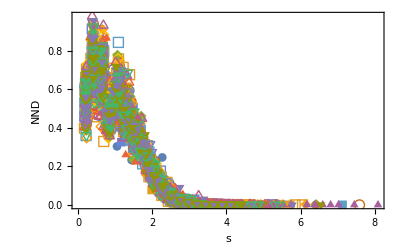

```mathematica
plotNND=ListPlot[Import[#,"Data"]&/@filesNND,PlotMarkers->Automatic, Frame->True,FrameLabel->{Style["s",FontFamily->"Times New Roman",Italic,15],Style["NND",FontFamily->"Times New Roman",Italic,15]}]
```

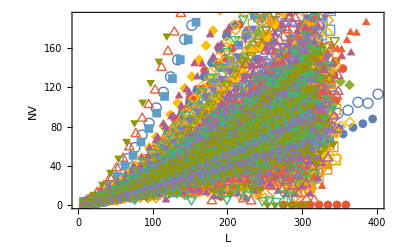

```mathematica
plotNV=ListPlot[Import[#,"Data"]&/@filesNV,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style["L",FontFamily->"Times New Roman",Italic,15],Style["NV",FontFamily->"Times New Roman",Italic,15]}]
```